{{a→(12 (-15+4 ⅇ+6 ⅇ^2))/(7 ⅇ^3),b→-(60 (-6+3 ⅇ+ⅇ^2))/(7 ⅇ^3),c→-(12 (10-12 ⅇ+3 ⅇ^2))/(7 ⅇ^3)}}

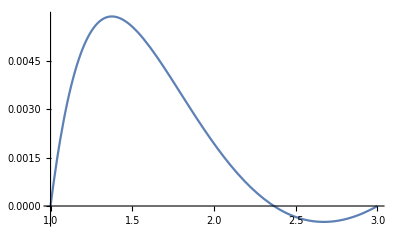

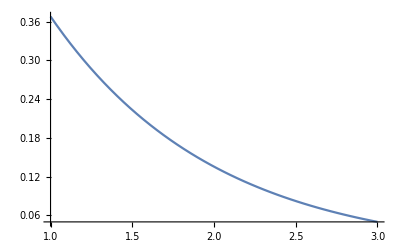

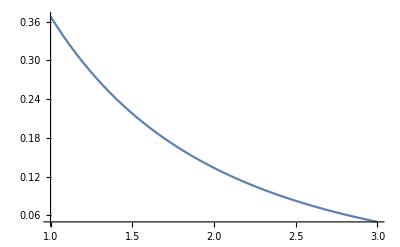

```mathematica
(*Да се построи обобщен полином по функциите f0(t)=1/(1+t), f1(t)=1/(2+t), f2(t)=1/(3+t) и интерполиращ f(t) = e^(-t), за t=1, t=2 и t=3.*)
f0[t_]:=1/(1+t);
f1[t_]:=1/(2+t);
f2[t_]:=1/(3+t);
f[t_]:=Exp[-t];
solution = Solve[{a*f0[1]+b*f1[1]+c*f2[1]==f[1],
                                   a*f0[2]+b*f1[2]+c*f2[1]==f[2],
	                          a*f0[3]+b*f1[3]+c*f2[3]==f[3]},{a,b,c}]
L[t_]:=Simplify[a*f0[t]+b*f1[t]+c*f2[t]/.solution];
Plot[f[t]-L[t],{t,1,3}]
Plot[f[t],{t,1,3}]
Plot[L[t],{t,1,3}]
```